```mathematica
fontName="Times";
SetOptions[Plot,FrameStyle->Directive[Thickness[0.002],13,fontName],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.001],Black],LabelStyle->(FontFamily->fontName),ImageSize->300,Frame->True,PlotStyle->Thick];
SetOptions[ParametricPlot,FrameStyle->Directive[Thickness[0.002],13,fontName],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.001],Black],LabelStyle->(FontFamily->fontName),ImageSize->400,Frame->True,PlotStyle->Thick];
SetOptions[ParametricPlot3D,
BoxStyle->Directive[Thickness[0.002],13,fontName],LabelStyle->(FontFamily->fontName),ImageSize->400];
SetOptions[ListPlot,FrameStyle->Directive[Thickness[0.002],13,fontName],GridLines->Automatic,GridLinesStyle->Directive[Thickness[0.001],Black],LabelStyle->(FontFamily->fontName),ImageSize->400,Frame->True,PlotStyle->Thick];
SetOptions[Histogram,FrameStyle->Directive[Thickness[0.002],13,fontName],LabelStyle->(FontFamily->fontName),ImageSize->600,Frame->True];
Traditional[expr_]:=TraditionalForm[If[ListQ[expr], Column[expr //. {x_[t] -> x, x_' ->ẋ}], expr //. {x_[t] -> x, x_' ->ẋ}]];
vRuleT={ψ[t]->ψ,φ[t]->φ,θ[t]->θ,θ'[t]->θ',φ'[t]->φ',ψ'[t]->ψ',x'[t]->x',y'[t]->y',z'[t]->z',a'[t]->a',α'[t]->α',β'[t]->β',x[t]->x,y[t]->y,z[t]->z,a[t]->a,α[t]->α,β[t]->β};TraditionalT[names_,expressions_] :=MapThread[Equal,{names,expressions}]/.vRuleT//TableForm//TraditionalForm;SetDirectory[NotebookDirectory[]];
```

```mathematica
r0={x[t],y[t]};
A={-a[t] Sin[α[t]],a[t] Cos[α[t]]};
L={-l Sin[α[t]-θ[t]],l Cos[α[t]-θ[t]]};
r3=r0+A;r2=r3+L;r1=r3-L;
R1=r1-r0;   R2=r2-r0;
v0=D[r0,t];
v1=D[r1,t];
v2=D[r2,t];v3=D[r3,t];
```

```mathematica
F3=-n/a[t]^3 A;
P=-p/a[t]A;
U0={Cos[α[t]](( Subscript[k, α] Sin[α[t]]+Subscript[k, αt] α'[t])+Subscript[k, x] x[t]+Subscript[k, xt] x'[t]),Sin[α[t]]((Subscript[k, α] Sin[α[t]]+Subscript[k, αt] α'[t])+Subscript[k, x] x[t]+Subscript[k, xt] x'[t])}//Simplify;
Series[U0,{α[t],0,1}];
F0=P-(F3)+U0;
```

```mathematica
ET=Subscript[m, 0] (v0.v0)/2+Subscript[m, 3] (v3.v3)/2+(J θ'[t]^2)/2//FullSimplify;
Collect[%,{x'[t],y'[t],α'[t],a'[t]}]//Simplify;
```

```mathematica
vars={r0,a[t],θ[t],α[t]}//Flatten;
vars1=Flatten[{r0,a[t],θ[t],α[t],α'[t]}];
Q=((D[r0,#].F0+D[r1,#].F1+D[r2,#].F2+D[r3,#].F3)&/@vars);
eq0=MapIndexed[D[D[ET,D[#1,t]],t]-D[ET,#1]==Q[[First[#2]]]&,vars]//Simplify;
params={Subscript[k, x]->.1 ,Subscript[k, xt]->.1,Subscript[k, α]->-5,Subscript[k, αt]->-2,Subscript[m, 0]->200,Subscript[m, 3]->1000,J->.001000,p->.2,n->0.008263297560335526,l->2};
tk=3600 24 5;
tk=3000;
```

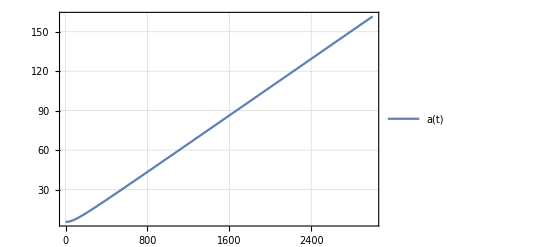
-Graphics-t,sa

```mathematica
params={Subscript[k, x]->.0 ,Subscript[k, xt]->.0,Subscript[k, α]->0,Subscript[k, αt]->0,Subscript[m, 0]->200,Subscript[m, 3]->1000,J->.001000,p->.0,n->0.008263297560335526,l->2};
sol=NDSolve[{eq0//.params,x[0]==0,y[0]==0,a[0]==5.4,θ[0]==0,α[0]==0,x'[0]==0,y'[0]==0,a'[0]==0,θ'[0]==0,α'[0]==0.01},vars1,{t,0,tk}, Method->{"EquationSimplification"->"Residual"}];
Labeled[Plot[{Evaluate[a[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"a(t)"}],{"t,s","a"},{Bottom,Left}]
Export["images/2sph_rev_no_u_a.png",%];
Labeled[Plot[{Evaluate[α[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"α(t)"}],{"t,s","α"},{Bottom,Left}];
Export["images/2sph_rev_no_u_alpha.png",%];
Labeled[Plot[{Evaluate[x[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"x(t)"}],{"t,s","x"},{Bottom,Left}];
Export["images/2sph_rev_no_u_x.png",%];
Labeled[Plot[{Evaluate[y[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"y(t)"}],{"t,s","y"},{Bottom,Left}];
Export["images/2sph_rev_no_u_y.png",%];
```

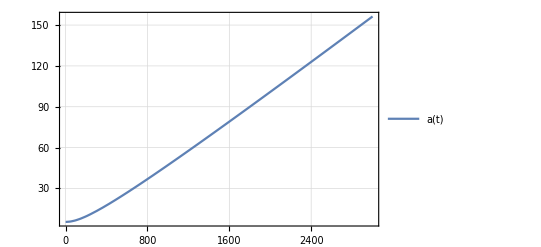
-Graphics-t,sa

```mathematica
params={Subscript[k, x]->.0 ,Subscript[k, xt]->.0,Subscript[k, α]->-5,Subscript[k, αt]->-2,Subscript[m, 0]->200,Subscript[m, 3]->1000,J->.001000,p->.0,n->0.008263297560335526,l->2};
sol=NDSolve[{eq0//.params,x[0]==0,y[0]==0,a[0]==5.4,θ[0]==0,α[0]==0,x'[0]==0,y'[0]==0,a'[0]==0,θ'[0]==0,α'[0]==0.01},vars1,{t,0,tk}, Method->{"EquationSimplification"->"Residual"}];
Labeled[Plot[{Evaluate[a[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"a(t)"}],{"t,s","a"},{Bottom,Left}]
Export["images/2sph_rev_alpha_u_a.png",%];
Labeled[Plot[{Evaluate[α[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"α(t)"}],{"t,s","α"},{Bottom,Left}];
Export["images/2sph_rev_alpha_u_alpha.png",%];
Labeled[Plot[{Evaluate[x[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"x(t)"}],{"t,s","x"},{Bottom,Left}];
Export["images/2sph_rev_alpha_u_x.png",%];
Labeled[Plot[{Evaluate[y[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"y(t)"}],{"t,s","y"},{Bottom,Left}];
Export["images/2sph_rev_alpha_u_y.png",%];
```

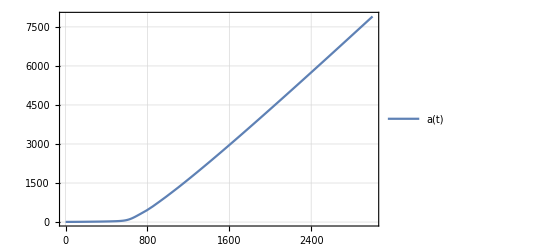
-Graphics-t,sa

```mathematica
params={Subscript[k, x]->.1 ,Subscript[k, xt]->.1,Subscript[k, α]->-5,Subscript[k, αt]->-2,Subscript[m, 0]->200,Subscript[m, 3]->1000,J->.001000,p->.0,n->0.008263297560335526,l->2};
sol=NDSolve[{eq0//.params,x[0]==0,y[0]==0,a[0]==5.4,θ[0]==0,α[0]==0,x'[0]==0,y'[0]==0,a'[0]==0,θ'[0]==0,α'[0]==0.01},vars1,{t,0,tk}, Method->{"EquationSimplification"->"Residual"}];
Labeled[Plot[{Evaluate[a[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"a(t)"}],{"t,s","a"},{Bottom,Left}]
Export["images/2sph_rev_full_u_a.png",%];
Labeled[Plot[{Evaluate[α[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"α(t)"}],{"t,s","α"},{Bottom,Left}];
Export["images/2sph_rev_full_u_alpha.png",%];
Labeled[Plot[{Evaluate[x[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"x(t)"}],{"t,s","x"},{Bottom,Left}];
Export["images/2sph_rev_full_u_x.png",%];
Labeled[Plot[{Evaluate[y[t]/.sol]},{t,0,tk},PlotRange->All,ImageSize->Full,PlotLegends->{"y(t)"}],{"t,s","y"},{Bottom,Left}];
Export["images/2sph_rev_full_u_y.png",%];
```